```mathematica
Presentation of the 2 Neuron circuit 

(*
==2 Neuron circuit==
the double-scroll attractor (sometimes known as Chua's attractor) is a strange attractor observed from a physical electronic chaotic circuit (generally,Chua's circuit) with a single nonlinear resistor (see Chua's Diode).The double-scroll system is often described by a system of three nonlinear ordinary differential equations and a 3-segment piecewise-linear equation (see Chua's equations).This makes the system easily simulated numerically and easily manifested physically due to Chua's circuits' simple design.
-http://www.chuacircuits.com/
-https://en.wikipedia.org/wiki/Multiscroll_attractor
dx/dt=c1*(y-x-f(x)) // m0: slope in outer region
   dy/dt=c2*(x-y+z)    // m1: slope in inner region
   dz/dt=-c3*y         // b: Breakpoints
   f(x)=m1*x+(m0-m1)/2*(|x+1|-|x-1|)
*)
```

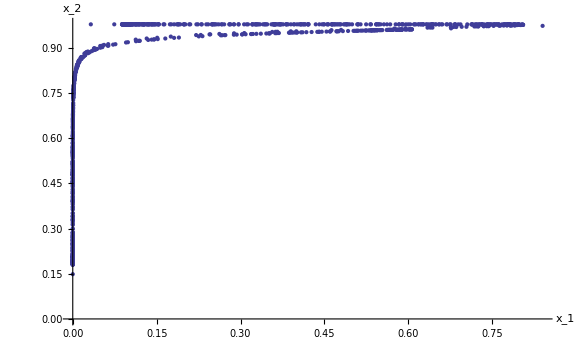

```mathematica
theta = {-3.4,3.8}; (* Neuron biases *)
w = {{-22.0,5.9},{-6.6,0}}; (* Neuron weights *)
x  = {0,0}; (* neuron activity states x_i(t) = [0,1] *)
c = {0,0}; (* control signals depending on the desired period (c_i = 0 is uncontrolled *)

p = 1;
Sigma[x_] := 1/(1+ Exp[-x]); (* Sigmoid function*)

neuronStep := Module[{y},
y = Sigma[theta + w.x + c];
x = y;
Return [x]];

limitedNeuronStep :=Module[{},Return[x]
];

n = 1000;
neuronPlot=Table[neuronStep,{i,1,n}];

ListPlot[neuronPlot,Axes->True,AxesLabel->{"x_1","x_2"},ImageSize->Large]
```